```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 361 Kb

{Utilities`CleanSlate`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
Clear[q]
q = { r[t], θ[t] }
```

{r[t],θ[t]}

```mathematica
Clear[s]
s = { r[t] Sin[θ[t]] , -r[t] Cos[θ[t]] }
```

{r[t] Sin[θ[t]],-Cos[θ[t]] r[t]}

```mathematica
D[s, t]
```

{Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t],-Cos[θ[t]] r'[t]+r[t] Sin[θ[t]] θ'[t]}

```mathematica
D[s, t] . D[s, t]
```

(Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t])^2+(-Cos[θ[t]] r'[t]+r[t] Sin[θ[t]] θ'[t])^2

```mathematica
D[s, t] . D[s, t]  // Expand
```

Cos[θ[t]]^2 r'[t]^2+Sin[θ[t]]^2 r'[t]^2+Cos[θ[t]]^2 r[t]^2 θ'[t]^2+r[t]^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[s, t] . D[s, t]  // Expand  // Simplify
```

r'[t]^2+r[t]^2 θ'[t]^2

```mathematica
Clear[T] 
T = 1/2 m ( D[s, t] . D[s, t]  // Expand  // Simplify  )
```

1/2 m (r'[t]^2+r[t]^2 θ'[t]^2)

```mathematica
Clear[V]
V = 1/2 k ( r[t] - l )^2- m g r[t] Cos[θ[t] ]
```

-g m Cos[θ[t]] r[t]+1/2 k (-l+r[t])^2

```mathematica
Clear[ℒ]
ℒ = T - V
```

g m Cos[θ[t]] r[t]-1/2 k (-l+r[t])^2+1/2 m (r'[t]^2+r[t]^2 θ'[t]^2)

```mathematica
D[D[ ℒ , D[q[[1]], t] ] ,t]- D[ ℒ,q[[1]]]
D[D[ ℒ , D[q[[2]], t] ] ,t]- D[ ℒ,q[[2]]]
```

-g m Cos[θ[t]]+k (-l+r[t])-m r[t] θ'[t]^2+m r''[t]

g m r[t] Sin[θ[t]]+2 m r[t] r'[t] θ'[t]+m r[t]^2 θ''[t]

```mathematica
Table[
D[D[ ℒ , D[q[[i]], t] ] ,t]- D[ ℒ,q[[i]]]== 0 ,
{i,1,2} ] // TableForm
```

-g m Cos[θ[t]]+k (-l+r[t])-m r[t] θ'[t]^2+m r''[t]==0
g m r[t] Sin[θ[t]]+2 m r[t] r'[t] θ'[t]+m r[t]^2 θ''[t]==0

```mathematica
Clear[eqs]
eqs = EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

k l+g m Cos[θ[t]]+r[t] (-k+m θ'[t]^2)-m r''[t]==0
-m r[t] (g Sin[θ[t]]+2 r'[t] θ'[t]+r[t] θ''[t])==0

```mathematica
Clear[parameters]
parameters = {
k-> 20 ,
g-> 9.8 , 
m -> 30,
l-> 5
} ;
parameters // TableForm
```

k→20
g→9.8
m→30
l→5

```mathematica
eqs /. parameters
```

{100+294. Cos[θ[t]]+r[t] (-20+30 θ'[t]^2)-30 r''[t]==0,-30 r[t] (9.8 Sin[θ[t]]+2 r'[t] θ'[t]+r[t] θ''[t])==0}

```mathematica
Clear[ics]
ics = { 
r[0] == 6 , 
r'[0] == 6,
θ[0] == π/6 ,
θ'[0] == 0.3
};
ics // TableForm
```

r[0]==6
r'[0]==6
θ[0]==π/6
θ'[0]==0.3

```mathematica
Clear[solution]
solution = NDSolve[ Union[ eqs /. parameters, ics] , q, { t, 0, 10 } ]
```

{{r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}}

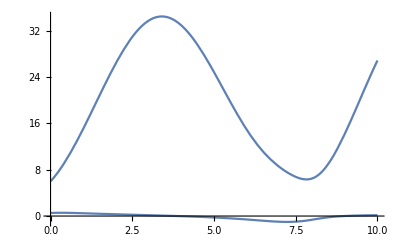

```mathematica
Plot[ q /. solution , { t, 0, 10 } ]
```

```mathematica
Exit[]
Quit[]
```